# Grover Search Algorithm

abtract

## Key Concepts

Boolean function

Grover Boolean oracle

Grover Phase oracle

Grover diffusion

## Statement of the Grover Search Problem

One of the most important quantum algorithms is Grover’s search algorithm. The problem can be stated as follows. Consider a Boolean function as follows:

Define a Boolean function

```mathematica
boo=(q1&&q2&&q3&&!q4&&!q5)||(q1&&q3&&q4&&q5);
```

Now let’s examine the truth table of the Boolean function above:

```mathematica
ResourceFunction["TruthTable"][boo,{q1,q2,q3,q4,q5}]
```

q1 | q2 | q3 | q4 | q5 | (q1&&q2&&q3&&!q4&&!q5)||(q1&&q3&&q4&&q5)
True | True | True | True | True | True
True | True | True | True | False | False
True | True | True | False | True | False
True | True | True | False | False | True
True | True | False | True | True | False
True | True | False | True | False | False
True | True | False | False | True | False
True | True | False | False | False | False
True | False | True | True | True | True
True | False | True | True | False | False
True | False | True | False | True | False
True | False | True | False | False | False
True | False | False | True | True | False
True | False | False | True | False | False
True | False | False | False | True | False
True | False | False | False | False | False
False | True | True | True | True | False
False | True | True | True | False | False
False | True | True | False | True | False
False | True | True | False | False | False
False | True | False | True | True | False
False | True | False | True | False | False
False | True | False | False | True | False
False | True | False | False | False | False
False | False | True | True | True | False
False | False | True | True | False | False
False | False | True | False | True | False
False | False | True | False | False | False
False | False | False | True | True | False
False | False | False | True | False | False
False | False | False | False | True | False
False | False | False | False | False | False

Let’s count the number of possible combinations of variable values that yield True when supplied as arguments to the Boolean function

```mathematica
ℳ=SatisfiabilityCount[boo]
```

3

The overall number of combination is 𝒩=2^5 (for n binary variables, you get 2^n possible combinations).

```mathematica
𝒩=2^5;
```

Therefore, if you try to guess the solution, your first guess will only be correct with the probability ℳ/𝒩 which is around 9%:

```mathematica
N[ℳ/𝒩]
```

0.09375

However, on your second guess, you should not repeat your first guess (since you will already know the status of your first guess). Thus, the probability to guess correctly will be ℳ/(𝒩-1) on the second guess. After you guess 𝒩-ℳ times, you are certain to know one of solutions. You could summarize the probability of at least one success within k tries as P_success(k)=1-(𝒩-ℳ
k)/(𝒩
k). Note that k is the number of times you tested the Boolean function, and by the time that k=𝒩-ℳ-1,  either you will have guessed the correct number or you will have eliminated all incorrect options.

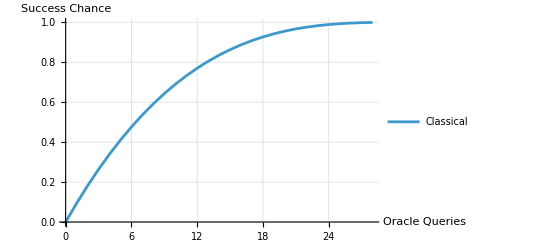

```mathematica
ListPlot[{Table[{k,1-Binomial[𝒩-ℳ,k]/Binomial[𝒩,k]},{k,0,𝒩-ℳ-1}]},Joined->True,AxesLabel->{"Oracle Queries","Success Chance"},PlotLegends->{"Classical"},GridLines->Automatic]
```

Grover’s key advantage can be illustrated as follows: by repeating the Grover circuit twice, the success probability can reach 100%, whereas a comparable classical strategy is about 20%.

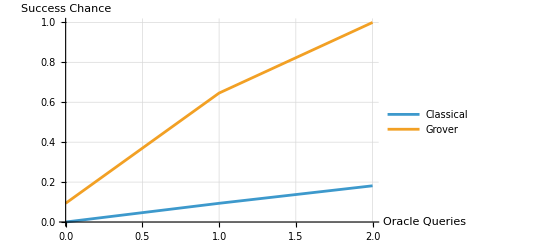

```mathematica
groverSuccess[N_,M_,k_]:=Sin[(2k+1)ArcCos[Sqrt[1-M/N]]]^2 
ListPlot[{Table[{k,1-Binomial[𝒩-ℳ,k]/Binomial[𝒩,k]},{k,0,2}],Table[{k,groverSuccess[𝒩,ℳ,k]},{k,0,2}]},Joined->True,AxesLabel->{"Oracle Queries","Success Chance"},PlotLegends->{"Classical","Grover"},GridLines->Automatic]
```

Another subtlety of Grover’s algorithm is that there is an optimal number of Grover iterations to maximize the success probability. As the illustration shows, the classical success probability increases monotonically with more queries, while Grover’s success oscillates and can decrease if you go past the optimum.

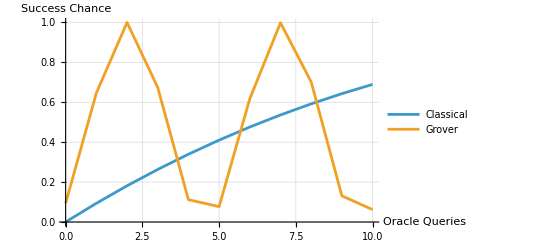

```mathematica
ListPlot[{Table[{k,1-Binomial[𝒩-ℳ,k]/Binomial[𝒩,k]},{k,0,10}],Table[{k,groverSuccess[𝒩,ℳ,k]},{k,0,10}]},Joined->True,AxesLabel->{"Oracle Queries","Success Chance"},PlotLegends->{"Classical","Grover"},GridLines->Automatic]
```

Let’s dive in and examine the details of Grover’s algorithm. We will set up the register, define the oracle, apply the Grover iterate (oracle plus diffusion), and analyze how repeated iterations amplify the marked states to enable high-probability retrieval of the solution.

## Grover oracle

Grover’s algorithm commonly uses two oracle types: the Boolean oracle and the phase oracle. Both encode information about the solution to a Boolean function. In the Boolean oracle, the solution is written to an ancillary (target) qubit. In the phase oracle, there is no ancilla; the solution is encoded in the phase. Let’s examine them in more details.

### Boolean oracle

The action of a Boolean oracle can be described as follows: it maps the state xq to xq⊕f(x), where x represents the n-qubit index register and q is an ancillary qubit holding the result of the Boolean function f(x). In this setup, if q=0, it flips to 1 when x satisfies f(x); otherwise, it remains unchanged. In other words, this oracle writes the value f(x) into a target qubit by XORing it into q.

Using the previous truth table, we can reproduce it with a quantum Boolean oracle. The oracle leaves the index register unchanged and flips the ancillary qubit exactly for inputs that satisfy the Boolean function, matching the table.

First, generate the corresponding Boolean oracle’s quantum circuit:

```mathematica
oracle=QuantumCircuitOperator["BooleanOracle"[boo]];
```

The diagram of the Boolean oracle:

```mathematica
oracle["Diagram",ImageSize->100]
```

-Graphics-

We initialize qubit 6 in the 0 state, and will use qubits 1–5 as the index register. To match the truth table, we will generate the index states x in descending order, from 2^n-1 down to 0.

```mathematica
n=oracle["Width"]-1;
states=QuantumTensorProduct[#,QuantumState["0"]]&/@Table[QuantumState["Register"[n,i]],{i,2^n-1,0,-1}];
```

Show how the oracle transforms states:

```mathematica
Row[Riffle[{oracle["Diagram",ImageSize->120,"WireLabels"->{n+1->"0"}],Sequence@@(TableForm[#,TableHeadings->{None, {"x,0","U_oracle x,0"}}]&/@Partition[Transpose[{TraditionalForm/@states,TraditionalForm[oracle[#]]&/@states}],10])},"   "]]
```

-Graphics-   x,0 | U_oracle x,0
111110 | 111111
111100 | 111100
111010 | 111010
111000 | 111001
110110 | 110110
110100 | 110100
110010 | 110010
110000 | 110000
101110 | 101111
101100 | 101100   x,0 | U_oracle x,0
101010 | 101010
101000 | 101000
100110 | 100110
100100 | 100100
100010 | 100010
100000 | 100000
011110 | 011110
011100 | 011100
011010 | 011010
011000 | 011000   x,0 | U_oracle x,0
010110 | 010110
010100 | 010100
010010 | 010010
010000 | 010000
001110 | 001110
001100 | 001100
001010 | 001010
001000 | 001000
000110 | 000110
000100 | 000100

As one can see, the Boolean oracle circuit reproduce the same result as the classical ones.

If the initial state of the ancillary qubit is -, the overall effect of the oracle will be adding - sign in front of x with x the solution of Boolean function. Let’s check that. First prepare qubit 1-5 in the register states and the target ancillary qubit in the minus state. This can be done by applying NOT gate and then Hadamard gate on the target qubit (qubit 6), using the states we have previously:

```mathematica
statesMinus=QuantumCircuitOperator[{"X"->n+1,"H"->n+1}]/@states;
```

Show the effect of the Boolean oracle on the new initial states:

```mathematica
Row[Riffle[{oracle["Diagram",ImageSize->120,"WireLabels"->{n+1->"-"}],Sequence@@(TableForm[#,TableHeadings->{None, {"x,-","U_oraclex,-"}}]&/@Partition[Transpose[{TraditionalForm[QuantumState[#,{Sequence@@ConstantArray[2,n],"X"}]]&/@statesMinus,TraditionalForm[QuantumState[oracle[#],{Sequence@@ConstantArray[2,n],"X"}]]&/@statesMinus}],10])},"   "]]
```

-Graphics-   x,- | U_oraclex,-
11111 𝓍_− | -11111 𝓍_−
11110 𝓍_− | 11110 𝓍_−
11101 𝓍_− | 11101 𝓍_−
11100 𝓍_− | -11100 𝓍_−
11011 𝓍_− | 11011 𝓍_−
11010 𝓍_− | 11010 𝓍_−
11001 𝓍_− | 11001 𝓍_−
11000 𝓍_− | 11000 𝓍_−
10111 𝓍_− | -10111 𝓍_−
10110 𝓍_− | 10110 𝓍_−   x,- | U_oraclex,-
10101 𝓍_− | 10101 𝓍_−
10100 𝓍_− | 10100 𝓍_−
10011 𝓍_− | 10011 𝓍_−
10010 𝓍_− | 10010 𝓍_−
10001 𝓍_− | 10001 𝓍_−
10000 𝓍_− | 10000 𝓍_−
01111 𝓍_− | 01111 𝓍_−
01110 𝓍_− | 01110 𝓍_−
01101 𝓍_− | 01101 𝓍_−
01100 𝓍_− | 01100 𝓍_−   x,- | U_oraclex,-
01011 𝓍_− | 01011 𝓍_−
01010 𝓍_− | 01010 𝓍_−
01001 𝓍_− | 01001 𝓍_−
01000 𝓍_− | 01000 𝓍_−
00111 𝓍_− | 00111 𝓍_−
00110 𝓍_− | 00110 𝓍_−
00101 𝓍_− | 00101 𝓍_−
00100 𝓍_− | 00100 𝓍_−
00011 𝓍_− | 00011 𝓍_−
00010 𝓍_− | 00010 𝓍_−

One can see that the oracle introduces a relative phase only on the terms that are solutions of the Boolean function.

Let’s verify that the final states are physically identical to the initial ones, since the oracle introduced only a global phase (which has no observable effect).

Create a list with elements as {x,-,U_oracle x,-}:

```mathematica
results=Transpose[{statesMinus,oracle/@statesMinus}];
```

Test {x,-,U_oracle x,-} are physically the same:

```mathematica
Apply[And][Equal@@@results]
```

True

As expected, only the solutions get a different phase shift. Note we have calculated that shift quantum mechanically.

### Phase oracle

Another common Grover oracle is the phase oracle. The key difference from the Boolean oracle is this: with a Boolean oracle, the solution is written to an ancillary (target) qubit; with a phase oracle, there is no ancilla and the solution is encoded as a phase. Let’s examine the phase oracle in more detail.

Create the corresponding phase oracle of the Boolean function:

```mathematica
phaseOracle=QuantumCircuitOperator["PhaseOracle"[boo]];
```

The diagram of oracle:

```mathematica
phaseOracle["Diagram",ImageSize->120]
```

-Graphics-

We initialize qubits 1–3 in the index register. As before to match the truth table, we will generate the index states x in descending order, from 2^n-1 down to 0.

```mathematica
With[{states=Table[QuantumState["Register"[n,i]],{i,2^n-1,0,-1}]},
Row[Riffle[{phaseOracle["Diagram",ImageSize->120,"WireLabels"->{n+1->"0"}],Sequence@@(TableForm[#,TableHeadings->{None, {"x","U_phase x"}}]&/@Partition[Transpose[{TraditionalForm/@states,TraditionalForm[phaseOracle[#]]&/@states}],8])},"   "]]]
```

-Graphics-   x | U_phase x
11111 | -11111
11110 | 11110
11101 | 11101
11100 | -11100
11011 | 11011
11010 | 11010
11001 | 11001
11000 | 11000   x | U_phase x
10111 | -10111
10110 | 10110
10101 | 10101
10100 | 10100
10011 | 10011
10010 | 10010
10001 | 10001
10000 | 10000   x | U_phase x
01111 | 01111
01110 | 01110
01101 | 01101
01100 | 01100
01011 | 01011
01010 | 01010
01001 | 01001
01000 | 01000   x | U_phase x
00111 | 00111
00110 | 00110
00101 | 00101
00100 | 00100
00011 | 00011
00010 | 00010
00001 | 00001
00000 | 00000

As one can see, the oracle circuit reproduce the same result as the classical ones, but this time the solution information is in the phase.

## Grover’s Algorithm

The full Grover search operation looks like this:

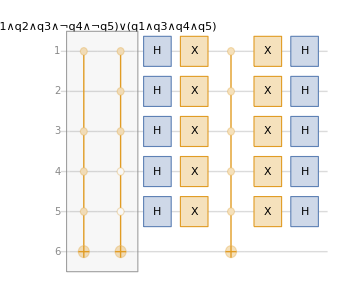

```mathematica
gs=QuantumCircuitOperator["Grover"[boo]];
gs["Diagram"]
```

The second block of gates is known as the Grover diffusion operator. The combination of the Boolean oracle and Grover diffusion operator are applied together in one iteration of the algorithm. To take advantage of the phase kickback introduced by the controlled gates, the circuit will need an initial set of gates and finally a measurement of the first three qubits.

One iteration of the Grover algorithm for the current example would look like this:

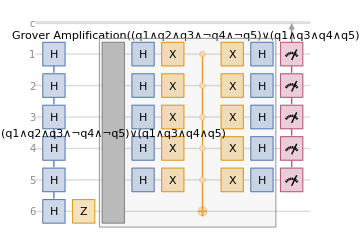

```mathematica
oneIteration=QuantumCircuitOperator[{"H"->Range[n+1],"Z"->n+1,gs,Range[n]}];
oneIteration["Diagram"]
```

The measurement distribution for this circuit is shown below:

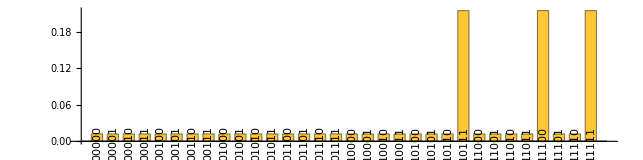

```mathematica
oneIteration[]["ProbabilitiesPlot","LabelsAngle"->90Degree,AspectRatio->1/4]
```

Recall that, for the states above, the Boolean function outputs are:

```mathematica
Thread[Tuples[{0,1},n]->Reverse[BooleanTable[boo]]]
```

{{0,0,0,0,0}→False,{0,0,0,0,1}→False,{0,0,0,1,0}→False,{0,0,0,1,1}→False,{0,0,1,0,0}→False,{0,0,1,0,1}→False,{0,0,1,1,0}→False,{0,0,1,1,1}→False,{0,1,0,0,0}→False,{0,1,0,0,1}→False,{0,1,0,1,0}→False,{0,1,0,1,1}→False,{0,1,1,0,0}→False,{0,1,1,0,1}→False,{0,1,1,1,0}→False,{0,1,1,1,1}→False,{1,0,0,0,0}→False,{1,0,0,0,1}→False,{1,0,0,1,0}→False,{1,0,0,1,1}→False,{1,0,1,0,0}→False,{1,0,1,0,1}→False,{1,0,1,1,0}→False,{1,0,1,1,1}→True,{1,1,0,0,0}→False,{1,1,0,0,1}→False,{1,1,0,1,0}→False,{1,1,0,1,1}→False,{1,1,1,0,0}→True,{1,1,1,0,1}→False,{1,1,1,1,0}→False,{1,1,1,1,1}→True}

Put simply, we only care about inputs that evaluate to True. A convenient trick is to map False → 0 and True → 1.

```mathematica
Thread[Tuples[{0,1},n]->Reverse[BooleanTable[boo]]/.{False->0,True->1}]
```

{{0,0,0,0,0}→0,{0,0,0,0,1}→0,{0,0,0,1,0}→0,{0,0,0,1,1}→0,{0,0,1,0,0}→0,{0,0,1,0,1}→0,{0,0,1,1,0}→0,{0,0,1,1,1}→0,{0,1,0,0,0}→0,{0,1,0,0,1}→0,{0,1,0,1,0}→0,{0,1,0,1,1}→0,{0,1,1,0,0}→0,{0,1,1,0,1}→0,{0,1,1,1,0}→0,{0,1,1,1,1}→0,{1,0,0,0,0}→0,{1,0,0,0,1}→0,{1,0,0,1,0}→0,{1,0,0,1,1}→0,{1,0,1,0,0}→0,{1,0,1,0,1}→0,{1,0,1,1,0}→0,{1,0,1,1,1}→1,{1,1,0,0,0}→0,{1,1,0,0,1}→0,{1,1,0,1,0}→0,{1,1,0,1,1}→0,{1,1,1,0,0}→1,{1,1,1,0,1}→0,{1,1,1,1,0}→0,{1,1,1,1,1}→1}

From the full measurement distribution, sum only the probabilities of inputs labeled True (1).

```mathematica
oneIteration[]["ProbabilitiesList"].(Reverse[BooleanTable[boo]]/.{False->0,True->1})//N
```

0.645996

As one can see, with the chance of around 65%, we can get the correct solution of the Boolean function by only one iteration of Grover.

Now what happens if two iterations are used instead of one?

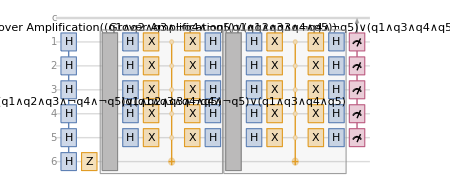

```mathematica
twoIteration=QuantumCircuitOperator[{"H"->Range[n+1],"Z"->n+1,gs,gs,Range[n]}];
twoIteration["Diagram",ImageSize->450]
```

The circuit is longer, but now the probability for obtaining the desired outcome is increased:

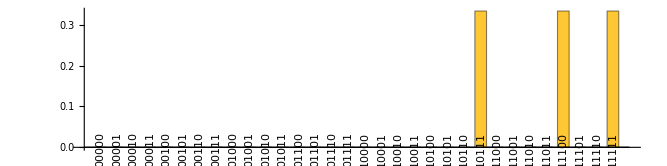

```mathematica
twoIteration[]["ProbabilitiesPlot","LabelsAngle"->90Degree,AspectRatio->1/4]
```

In this case, with the chance of most 100%, we can get the correct solution of the Boolean function by only two iterations of Grover.

```mathematica
twoIteration[]["ProbabilitiesList"].(Reverse[BooleanTable[boo]]/.{False->0,True->1})//N
```

0.999779

We can also calculate the success probability given the number of Grover iteration:

```mathematica
successProabGrover=MapIndexed[{#2[[1]]-1,#1["ProbabilitiesList"].Flatten[Reverse[BooleanTable[boo]]/.{False->{0,0},True->{1,1}}]}&,NestList[N[gs],QuantumState["+++++-"],10]];
```

As you can see, the probability rises then falls and rises again as more and more Grover iterations are applied.

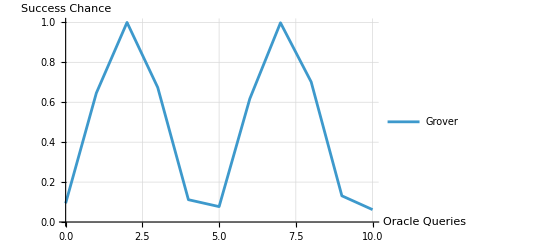

```mathematica
ListPlot[successProabGrover,Joined->True,AxesLabel->{"Oracle Queries","Success Chance"},PlotLegends->{"Grover"},GridLines->Automatic]
```

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]